```mathematica
p={α,β,δ,γ}={1.1,0.4,0.1,0.4} ;
{x0,y0}={10.0,10.0};
{x02,y02}={11.0,11.0};
```

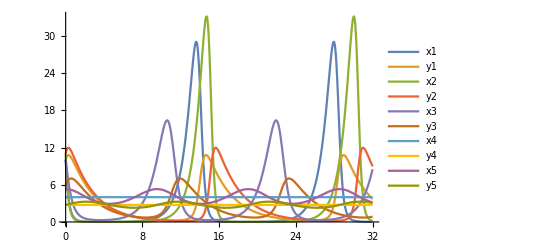

```mathematica
TMax=32;
{xSol1,ySol1}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==x0,
y[0]==y0 
},
{x,y}, {t, 0, TMax}];
{xSol2,ySol2}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==x02,
y[0]==y02
},
{x,y}, {t, 0, TMax}];
{xSol3,ySol3}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==10.0,
y[0]==6.0
},
{x,y}, {t, 0, TMax}];
{xSol4,ySol4}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==γ/δ,
y[0]==α/β
},
{x,y}, {t, 0, TMax}];
{xSol5,ySol5}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==γ/δ +1.3,
y[0]==α/β
},
{x,y}, {t, 0, TMax}];
Plot[{xSol1[t],ySol1[t],xSol2[t],ySol2[t],xSol3[t],ySol3[t],
xSol4[t],ySol4[t],xSol5[t],ySol5[t]},{t, 0, TMax},
PlotRange->All,
PlotLegends->{"x1","y1","x2","y2","x3","y3","x4","y4","x5","y5"}]
```

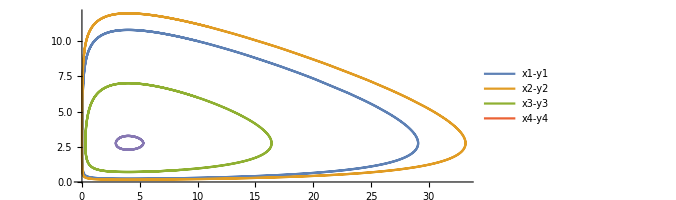

```mathematica
Pic=ParametricPlot[{{xSol1[t],ySol1[t]},
{xSol2[t],ySol2[t]},
{xSol3[t],ySol3[t]},
{xSol4[t],ySol4[t]},
{xSol5[t],ySol5[t]}
},
{t, 0, TMax},
PlotRange->All,
PlotLegends->{"x1-y1","x2-y2","x3-y3","x4-y4"}]
```